General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

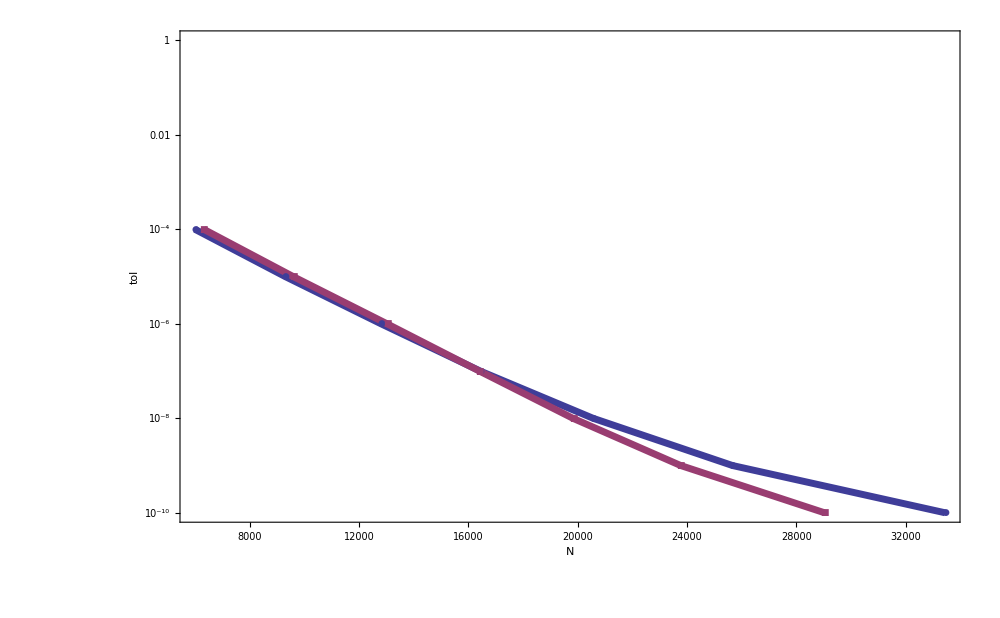

```mathematica
(*1_1*)
NN={4,5,6,7,8,9,10};
NN=10.^-#&/@NN;

step={5997,9298,12805,16434,20565,25667,33444};
twostep={6319,9589,13024,16404,19826,23771,29033};
Needs["PlotLegends`"]
gp[NN_,arr_]:=Partition[Riffle[NN,arr],2];
g1=ListLogPlot[{gp[step,NN],gp[twostep,NN]},LabelStyle->Directive[Bold,FontSize->20,Black],Frame->True,PlotMarkers->Automatic ,Joined->True,PlotStyle->{{Directive[PointSize[.4]],Thickness[0.005]}},Axes->False,PlotLegendStyle->{Large},PlotLegend->{Style["STEPSIZE h",20,Bold],Style["STEPSIZE 2h",20,Bold]},LegendPosition->{1.1,-0.4},Joined->{True,True,False},PlotMarkers->Automatic,FrameLabel->{"N","tol"},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->1000]
(*Export["/home/geldor/num_ex_1_1.pdf",g1]*)
```

```mathematica
NN//ScientificForm
```

{1.×10^-4,1.×10^-5,1.×10^-6,1.×10^-7,1.×10^-8,1.×10^-9,1.×10^-10}

```mathematica
Options[ListPlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→False,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}

```mathematica
10^10
```

10000000000